```mathematica
Solve[T^2+T-1==0,T]//N
```

{{T→-1.61803},{T→0.618034}}

```mathematica
m =({{1, T, T, T, 1}, {1, 0, 0, 0, -1}, {T, 1, T, 0, 0}, {0, T, 1, T, 0}, {0, 0, T, 1, T}})(*small, 5x5*)
```

{{1,T,T,T,1},{1,0,0,0,-1},{T,1,T,0,0},{0,T,1,T,0},{0,0,T,1,T}}

```mathematica
me=Transpose@Append[Transpose[m],{e,0,b,b,b}]
```

{{1,T,T,T,1,e},{1,0,0,0,-1,0},{T,1,T,0,0,b},{0,T,1,T,0,b},{0,0,T,1,T,b}}

```mathematica
m =({{1, 1, 1, 1, 1, 1}, {1, 0, 0, 0, 0, -1}, {T, 1, T, 0, 0, 0}, {0, T, 1, T, 0, 0}, {0, 0, T, 1, T, 0}, {0, 0, 0, T, 1, T}}); (*big, 6x6*)
Det[m]//Factor
T/.Solve[Det[m]==0,T]//N
```

-2 (-1+T) (1+T) (-1+T+T^2)

{-1.,1.,-1.61803,0.618034}

```mathematica
m =({{1, 1, 1, 1, 1, 1}, {-d, -4, 1, 0, 1, -4}, {1, 2, 3, 4, 5, d}, {2, 1, 2, 1, 1, 1}, {-d, 1, d, 1, 0, 0}, {0, 0, 1, 2, 2d, 0}});(*new big 6x6*)
Det[m]//Factor
d/.Solve[Det[m]==0,d]//N
```

2 (-10+32 d-29 d^2+8 d^3)

{0.529386,1.36211,1.7335}

```mathematica
me=Transpose@Append[Transpose[m],{e,q,q,q,q,q}];
MatrixForm[me]
```

(1 | 1 | 1 | 1 | 1 | 1 | e
-d | -4 | 1 | 0 | 1 | -4 | q
1 | 2 | 3 | 4 | 5 | d | q
2 | 1 | 2 | 1 | 1 | 1 | q
-d | 1 | d | 1 | 0 | 0 | q
0 | 0 | 1 | 2 | 2 d | 0 | q)

```mathematica
Det[m]//Factor
```

-2 (-2+T) (-1+T) T (1+T)

```mathematica
NSolve[Det[m]==0,T]
```

{{T→-1.},{T→0.},{T→1.},{T→2.}}

```mathematica
T=.
```

```mathematica
RowReduce[me]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | (-25 e-7 d e+21 d^2 e-4 d^3 e+24 d q-21 d^2 q+4 d^3 q)/(-10+32 d-29 d^2+8 d^3)
0 | 1 | 0 | 0 | 0 | 0 | (35 e-163 d e+112 d^2 e-16 d^3 e+2 d^4 e-20 q+76 d q-53 d^2 q+12 d^3 q-2 d^4 q)/(2 (-10+32 d-29 d^2+8 d^3))
0 | 0 | 1 | 0 | 0 | 0 | (35 e-25 d e+8 d^2 e-4 d^3 e-10 q+8 d q-8 d^2 q+4 d^3 q)/(-10+32 d-29 d^2+8 d^3)
0 | 0 | 0 | 1 | 0 | 0 | (-35 e+43 d e-76 d^2 e+42 d^3 e-2 d^4 e+8 d q+27 d^2 q-22 d^3 q+2 d^4 q)/(2 (-10+32 d-29 d^2+8 d^3))
0 | 0 | 0 | 0 | 1 | 0 | (-9 e+34 d e-19 d^2 e+d^3 e+8 q-24 d q+13 d^2 q-d^3 q)/(-10+32 d-29 d^2+8 d^3)
0 | 0 | 0 | 0 | 0 | 1 | (-11 e+90 d e-57 d^2 e+2 d^3 e+12 q-50 d q+29 d^2 q-2 d^3 q)/(-10+32 d-29 d^2+8 d^3))

```mathematica
e=.
```

```mathematica
RowReduce[me,ZeroTest->Function[ex,Reduce[ex==0,{T,e,b},Reals] =!=False]]//Expand//MatrixForm
```

(1 | 0 | 0 | 0 | -3+2 d | 2-d | 2 e
0 | 1 | 0 | 0 | 5/2-2 d | d/2 | e/2-q
0 | 0 | 1 | 0 | 3-2 d | -2+d | -3 e+q
0 | 0 | 0 | 1 | -3/2+2 d | 1-d/2 | (3 e)/2
0 | 0 | 0 | 0 | 2+12 d-8 d^2 | 2-8 d+4 d^2 | 4 e-10 d e-4 q+2 d q
0 | 0 | 0 | 0 | -16+18 d-4 d^2 | 4-6 d+2 d^2 | -10 e-4 d e+8 q)

```mathematica
RowReduce[me]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | (-t+e T)/T
0 | 1 | 0 | 0 | 0 | 0 | (t-2 b T-t T+b T^2+e T^2-t T^2-2 b T^3+e T^3+t T^3+b T^4-e T^4)/(T (-1+T^2) (-1-T+T^2))
0 | 0 | 1 | 0 | 0 | 0 | (t+b T-e T+3 b T^2-e T^2-t T^2-3 b T^3+e T^3+b T^4)/(T (-1+T^2) (-1-T+T^2))
0 | 0 | 0 | 1 | 0 | 0 | (t-3 b T+b T^2)/(T (-1-T+T^2))
0 | 0 | 0 | 0 | 1 | 0 | (-t+e T+t T-5 b T^2+e T^2+t T^2+2 b T^3-e T^3-t T^3+b T^4)/(T (-1+T^2) (-1-T+T^2))
0 | 0 | 0 | 0 | 0 | 1 | (-t+2 b T-4 b T^2+e T^2+t T^2)/(T (-1+T^2)))

```mathematica
TrueQ[T==0]
```

False

```mathematica
Function[e,Reduce[e==0,#1,Reals] =!=False]&[T][1-T^2]
```

True

```mathematica
T=2.879385241571817
```

2.87939

```mathematica
T=.
```

```mathematica
(meset = me/.T->1.618033988749895)//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | e
1 | 0 | 0 | 0 | 0 | -1 | 0
1 | 1.61803 | 1 | 0 | 0 | 0 | b
0 | 1 | 1.61803 | 1 | 0 | 0 | b
0 | 0 | 1 | 1.61803 | 1 | 0 | b
0 | 0 | 0 | 1 | 1.61803 | 1 | b)

```mathematica
RowReduce[meset,ZeroTest->Function[ex,Reduce[ex==0,{e,b,T},Reals] =!=False||Chop[ex,0.001]===0]]//FullSimplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | -1.38197 b+1. e
0 | 1 | 0 | 0 | 1. | 0 | 3.23607 b-1.61803 e
0 | 0 | 1 | 0 | -1.61803 | 0 | -2.8541 b+1.61803 e
0 | 0 | 0 | 1 | 1.61803 | 0 | 2.38197 b-1. e
0 | 0 | 0 | 0 | 4.44089×10^-16 | 1 | -1.38197 b+1. e
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Chop[0.000001,0.001]===0
```

```mathematica
RowReduce[meset]//MatrixForm
```

(1 | 0 | 0 | 0 | 0. | 0 | 4.61803 b
0 | 1 | 0 | 0 | 1. | 0 | -6.47214 b
0 | 0 | 1 | 0 | -1.61803 | 0 | 6.8541 b
0 | 0 | 0 | 1 | 1.61803 | 0 | -3.61803 b
0 | 0 | 0 | 0 | 0. | 1 | 4.61803 b
0 | 0 | 0 | 0 | 0. | 0 | 0.)

```mathematica
RowReduce[m//N,ZeroTest->(Chop[#,0.001]===0&)]//MatrixForm
```

(1 | 0 | 0 | 0 | -1.
0 | 1 | 0 | 0 | -0.184793
0 | 0 | 1 | 0 | 1.06418
0 | 0 | 0 | 1 | -0.184793
0 | 0 | 0 | 0 | 0)

```mathematica
RowReduce[m]//MatrixForm
```

(1 | 0. | 0. | 0. | -1.
0 | 1 | 0. | 0. | -0.184793
0 | 0 | 1 | 0. | 1.06418
0 | 0 | 0 | 1 | -0.184793
0 | 0 | 0 | 0 | 0)

```mathematica
Chop[0.0001,0.001]===0
```

True

```mathematica
me//MatrixForm
```

(1 | 2.87939 | 2.87939 | 2.87939 | 1 | e
1 | 0 | 0 | 0 | -1 | 0
2.87939 | 1 | 2.87939 | 0 | 0 | b
0 | 2.87939 | 1 | 2.87939 | 0 | b
0 | 0 | 2.87939 | 1 | 2.87939 | b)

```mathematica
Solve[(1-T^2)==(2T+1-T^3),T]//N
```

{{T→-1.},{T→0.},{T→2.}}

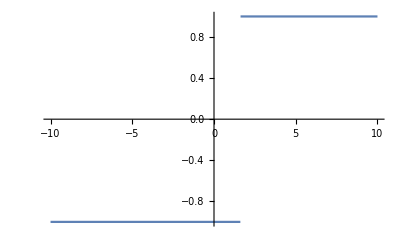

```mathematica
Plot[Sign[T^3-1-2T ],{T,-10,10}]
```

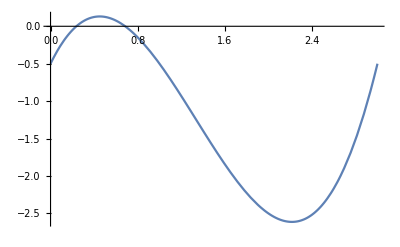

```mathematica
Plot[T^3-1-2T +(5T-4T^2+0.5),{T,0,3}]
```

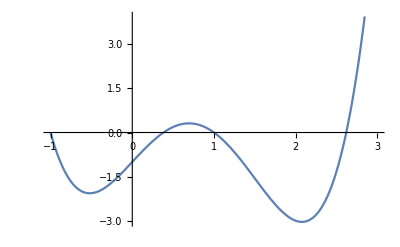

```mathematica
Plot[(1-T)(2T+1-T^3)-(1-T^2)(2-2T),{T,-1,3}]
```

```mathematica
p[T_]:=Expand[(1-T^2)(T^2+T-5)-(2T+1-T^3)];
p[T]
```

-6-T+6 T^2-T^4

```mathematica
Solve[p[T]==0,T]//N
```

{{T→-1.},{T→2.},{T→-2.30278},{T→1.30278}}

```mathematica
d=.
```

```mathematica
m =({{1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 2-2T b, 1}, {1, T b, 1, 0, 0, 0}, {0, 1, T b, 1, 0, 0}, {0, 0, 1, T b, 1, 0}, {0, 0, 0, 1, T b, 1}});(*new big 6x6*)
Det[m]//Expand
T/.Solve[Det[m]==0,T]//N
```

-1+5 b T-2 b^2 T^2-5 b^3 T^3+3 b^4 T^4

{-1./b,1/b,0.232408/b,1.43426/b}

```mathematica
m2=m/.T->2
```

{{1,1,1,1,1,1},{0,0,0,0,1,1},{1,2,1,0,0,0},{0,1,2,1,0,0},{0,0,1,2,1,0},{0,0,0,1,2,1}}

```mathematica
m =({{1, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 2-2T, 1}, {1, T, 1, 0, 0, 0}, {0, 1, T, 1, 0, 0}, {0, 0, 1, T, 1, 0}, {0, 0, 0, 1, T, 1}});(*new big 6x6*)
Det[m]//Expand
T/.Solve[Det[m]==0,T]//N
me=Transpose@Append[Transpose[m],{e,mag,b,b,b,b}];
MatrixForm[me]
```

-1+5 T-2 T^2-5 T^3+3 T^4

{-1.,1.,0.232408,1.43426}

(1 | 1 | 1 | 1 | 1 | 1 | e
0 | 0 | 0 | 0 | 2-2 T | 1 | mag
1 | T | 1 | 0 | 0 | 0 | b
0 | 1 | T | 1 | 0 | 0 | b
0 | 0 | 1 | T | 1 | 0 | b
0 | 0 | 0 | 1 | T | 1 | b)

```mathematica
Det@m
```

-1+5 T-2 T^2-5 T^3+3 T^4

```mathematica
RowReduce[m/.sol[[2]],ZeroTest->Function[ex,Reduce[ex==0,{T,e,q,t},Reals] =!=False]]//Simplify//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | -3/(1+√13)
0 | 0 | 1 | 0 | 0 | 1/4 (-7+√13)
0 | 0 | 0 | 1 | 0 | 1/4 (7-√13)
0 | 0 | 0 | 0 | 1 | 3/(1+√13)
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Solve[1+(1-T) T-T (T+(1-T) T^2)==0,T]
```

{{T→-1},{T→1},{T→1/2 (1-√5)},{T→1/2 (1+√5)}}

```mathematica
e-(1+T)b+(1-T)b(-T^2+T-1)-(1-T^2)b /√5/.sol//Simplify//Column
```

-2 b+e
-1/270 (485-3 √5+5 √13+15 √65) b+e
1/270 (-485+3 √5+5 √13+15 √65) b+e

```mathematica
(rrme=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {-1, T-1, -((-1+T) T), -(T-(-1+T) T^2), -(1-T-T^2+T^3), 1}}).({{0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}, {0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}}).me)//Expand//MatrixForm
```

(1 | T | 1 | 0 | 0 | 0 | b
0 | 1 | T | 1 | 0 | 0 | b
0 | 0 | 1 | T | 1 | 0 | b
0 | 0 | 0 | 1 | T | 1 | b
0 | 0 | 0 | 0 | 2-2 T | 1 | mag
0 | 0 | 0 | 0 | -1+5 T-2 T^2-5 T^3+3 T^4 | 0 | -2 b+e-mag+b T+mag T-2 b T^2+mag T^2+b T^3-mag T^3)

```mathematica
sols=Solve[{{0, -1+5 T-2 T^2-5 T^3+3 T^4}}==0,T]
```

{{T→-1},{T→1},{T→1/6 (5-√13)},{T→1/6 (5+√13)}}

```mathematica
sol=sols[[{2,3,4}]]
```

{{T→1},{T→1/6 (5-√13)},{T→1/6 (5+√13)}}

```mathematica
rrme[[6]]/.sol//N//Column
```

{0.,0.,0.,0.,0.,0.,-2. b+e}
{0.,0.,0.,0.,0.,0.,-1.86307 b+e-0.726132 mag}
{0.,0.,0.,0.,2.22045×10^-16,-4.44089×10^-16,-1.72953 b+e-0.459054 mag}

```mathematica
m =({{1, 1, 1, 1, 1}, {0, 0, 0, 2-2T, 1}, {1, T, 1, 0, 0}, {0, 1, T, 1, 0}, {0, 0, 1, T, 1}});(*new big 6x6*)
Det[m]//Expand
T/.Solve[Det[m]==0,T]//N
me=Transpose@Append[Transpose[m],{e,b/√5,b,b,b}];
MatrixForm[me]
```

-2+T+5 T^2-3 T^3

{0.666667,-0.618034,1.61803}

(1 | 1 | 1 | 1 | 1 | e
0 | 0 | 0 | 2-2 T | 1 | b/(√5)
1 | T | 1 | 0 | 0 | b
0 | 1 | T | 1 | 0 | b
0 | 0 | 1 | T | 1 | b)

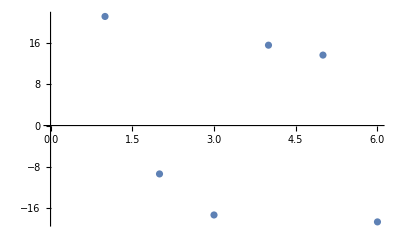

```mathematica
LinearSolve[m/.T->0.3, {5,1/√5,1,1,1,1}]//ListPlot
```

```mathematica
(3T^4-5T^3-2T^2+5T-1)RowReduce[me]/.{mag->0,e->1,b->1}//FullSimplify//Expand//MatrixForm
```

(-1+5 T-2 T^2-5 T^3+3 T^4 | 0 | 0 | 0 | 0 | 0 | -1-4 T+13 T^2-8 T^3+T^4
0 | -1+5 T-2 T^2-5 T^3+3 T^4 | 0 | 0 | 0 | 0 | 2-5 T+2 T^3
0 | 0 | -1+5 T-2 T^2-5 T^3+3 T^4 | 0 | 0 | 0 | 7 T-10 T^2+3 T^3
0 | 0 | 0 | -1+5 T-2 T^2-5 T^3+3 T^4 | 0 | 0 | -3+10 T-9 T^2+3 T^3
0 | 0 | 0 | 0 | -1+5 T-2 T^2-5 T^3+3 T^4 | 0 | -1+T-2 T^2+T^3
0 | 0 | 0 | 0 | 0 | -1+5 T-2 T^2-5 T^3+3 T^4 | 2-4 T+6 T^2-6 T^3+2 T^4)

```mathematica
(25+√13)/18//N
```

1.5892

```mathematica
RowReduce[me/.{T->(5+√13)/6,e->20,mag->18.325},ZeroTest->Function[ex,Reduce[ex==0,{b},Reals] =!=False]]//FullSimplify//Expand//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1 | 31.4135-1.18858 b
0 | 1 | 0 | 0 | 0 | 1/4+(√13)/4 | 1.72787+0.622839 b
0 | 0 | 1 | 0 | 0 | -7/4-(√13)/4 | -22.3039-0.434259 b
0 | 0 | 0 | 1 | 0 | 7/4+(√13)/4 | 30.2617+b
0 | 0 | 0 | 0 | 1 | -3/(-1+√13) | -21.0992
0 | 0 | 0 | 0 | 0 | 0 | 10.0642-1.50212 b)

```mathematica
Solve[28/81-(22 √13)/81+(29 mag)/81-(17 √13 mag)/81==0,mag]//FullSimplify
```

{{mag→1/18 (-25-√13)}}

```mathematica
(10.0642386131066-1.502123611083154 b)*3.76759/1.50212//Expand
```

25.2429-3.7676 b

```mathematica
Solve[10.0642386131066-1.502123611083154 b==0,b]
```

{{b→6.70001}}

```mathematica
((T^3-T^2-T+1)(18.325)-20)/(T^3-2T^2+T-2)/.T->1.4343
```

6.69923

```mathematica
((-T^3+T^2+T-1)(18.325)+20)/(-(T^3-2T^2+T-2))/.T->1.4343
```

6.69923

```mathematica
NSolve[-b+e-b(1-T)+b(1-T)T-mu(1-T-(1-T)T^2)-b(T+(1-T)T^2)==0/.T->1.43/.e->k,b]//Expand
```

{{b→0.576172 k-0.258878 mu}}

```mathematica
{b,0.5761719481468293 k-0.25887808950600727 mu}*1.73559//Expand
```

{1.73559 b,0.999998 k-0.449306 mu}

```mathematica
m={
{1,1,1,1,e},
{1,T,1,0,b},
{0,1,T,1,b},
{0,0,2(1-T),1,mu}
};
m[[1]]-=m[[2]];
m[[1]]-=(1-T)m[[3]];
m[[1]]-=T m[[4]];
MatrixForm[Expand[m]]
```

(0 | 0 | -3 T+3 T^2 | 0 | -2 b+e+b T-mu T
1 | T | 1 | 0 | b
0 | 1 | T | 1 | b
0 | 0 | 2-2 T | 1 | mu)

```mathematica
MatrixForm[m]/.T->0
```

(0 | 0 | 0 | 0 | -2 b+e
1 | 0 | 1 | 0 | b
0 | 1 | 0 | 1 | b
0 | 0 | 2 | 1 | mu)

```mathematica
MatrixForm[m]/.T->1
```

(0 | 0 | 0 | 0 | -b+e-mu
1 | 1 | 1 | 0 | b
0 | 1 | 1 | 1 | b
0 | 0 | 0 | 1 | mu)